## Export

```mathematica
$ExportFormats
```

{3DS,AC,ACO,AIFF,ASE,AU,AVI,Base64,Binary,Bit,BLEND,BMP,BREP,BSON,Byte,BYU,BZIP2,C,CDF,CDXML,Character16,Character32,Character8,CML,Complex128,Complex256,Complex64,CSV,Cube,CUR,DAE,DICOM,DIF,DIMACS,DOT,DTA,DXF,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FBX,FCS,FITS,FLAC,FLV,FMU,GeoJSON,GIF,GLTF,Graph6,Graphlet,GraphML,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTMLFragment,HTTPRequest,HTTPResponse,ICNS,ICO,IFC,IGES,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,ISO,JavaProperties,JavaScriptExpression,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LEDA,List,LWO,LXO,MAT,MathML,Matroska,Maya,MCTT,MGF,MIDI,MO,MOL,MOL2,MP3,MP4,MS3D,MTX,MX,MXNet,NASACDF,NB,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,OFF,Ogg,ONNX,OpenEXR,OWLFunctional,Pajek,PBM,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,POR,POV,PPM,PXR,PythonExpression,QuickTime,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RTF,SAS7BDAT,SAV,SCT,SDF,SMA,SMILES,SND,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STEP,STL,String,SurferGrid,SVG,Table,TAR,TerminatedString,TeX,TeXFragment,Text,TGA,TGF,TIFF,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USD,UUE,VideoFrames,VRML,VTK,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XGL,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZPR,ZSTD}

```mathematica
$ExportFormats//Length
```

204

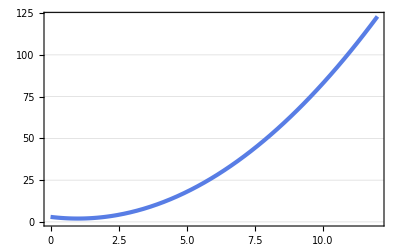

```mathematica
plot=Plot[(x-2)^2+2x -1, {x,0,12},PlotTheme->"Business"]
```

```mathematica
Export["plot.pdf",plot]
```

plot.pdf

```mathematica
$HomeDirectory
```

/home/jam

```mathematica
Export[NotebookDirectory[]<>"plot.pdf",plot]
```

/home/jam/Kuweta/mma_lessons/code/plot.pdf

```mathematica
Directory[]
```

/home/jam

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/mma_lessons/code

## Import

```mathematica
$ImportFormats
```

{3DS,7z,AC,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,ASC,ASE,AU,AVI,Base64,BDF,Binary,BioImageFormat,Bit,BLEND,BMP,BREP,BSON,Byte,BYU,BZIP2,CDED,CDF,CDX,CDXML,Character16,Character32,Character8,CIF,CML,Complex128,Complex256,Complex64,CSV,Cube,CUR,DAE,DBF,DICOM,DICOMDIR,DIF,DIMACS,Directory,DOCX,DOT,DTA,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FBX,FCHK,FCS,FITS,FLAC,FLV,GaussianLog,GenBank,GeoJSON,GeoTIFF,GIF,GLTF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXF,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,IFC,IGES,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,ISO,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LaTeX,LEDA,List,LWO,LXO,MAT,MathML,Matroska,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOBI,MOL,MOL2,MP3,MP4,MPS,MS3D,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,ODS,OFF,Ogg,ONNX,OpenEXR,OSM,OWLFunctional,Pajek,PBM,PCAP,PCX,PDB,PDF,PEM,PGM,PHPIni,PLY,PNG,PNM,POR,PPM,PXR,PythonExpression,QuickTime,RAR,Raw,RawBitmap,RawJSON,RData,RDFXML,RDS,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SAS7BDAT,SAV,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STEP,STL,String,SurferGrid,SVG,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USD,USGSDEM,UUE,VCF,VCS,VideoFormat,VTK,WARC,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XGL,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZSTD}

```mathematica
music=Import["https://upload.wikimedia.org/wikipedia/commons/f/ff/Vivaldi_-_Four_Seasons_1_Spring_mvt_1_Allegro_-_John_Harrison_violin.oga"]
```

```mathematica
Options[music,MetaInformation]
```

{MetaInformation→<|Xiph→<|Album→{Vivaldi: The Four Seasons},Artist→{John Harrison - Violin},COMMENT→{John Harrison, Violin\r
Robert Turizziani, Conductor\r
Wichita State University Chamber Players\r
http://JohnHarrisonViolin.com},RecordingDate→{Sun 6 Feb 2000},Genre→{Baroque},REPLAYGAIN_ALBUM_GAIN→{-0.05 decibels},REPLAYGAIN_ALBUM_PEAK→{1.10195 decibels},REPLAYGAIN_TRACK_GAIN→{0.73 decibels},REPLAYGAIN_TRACK_PEAK→{1.00085 decibels},Title→{Spring Mvt 1: Allegro},TrackNumber→{1}|>|>}

```mathematica
Export["Vivaldi_-_Four_Seasons_1_Spring_mvt_1_Allegro_-_John_Harrison_violin.mp3", music]
```

Export::unsmeta: Some or all of the supplied metadata are not supported by the MP3 format and will not be stored in the file.

Vivaldi_-_Four_Seasons_1_Spring_mvt_1_Allegro_-_John_Harrison_violin.mp3

```mathematica
music= Import["Vivaldi_-_Four_Seasons_1_Spring_mvt_1_Allegro_-_John_Harrison_violin.mp3"]
```

```mathematica
Export["music.mp3", music]
```

music.mp3

```mathematica
Options[music]
```

{Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1}

```mathematica
music//FullForm
```

Audio["music.oga","Real32",Rule[Appearance,Automatic],Rule[AudioOutputDevice,Automatic],Rule[MetaInformation,Association[Rule["Xiph",Association[Rule["Album",List["Vivaldi: The Four Seasons"]],Rule["Artist",List["John Harrison - Violin"]],Rule["COMMENT",List["John Harrison, Violin\r
Robert Turizziani, Conductor\r
Wichita State University Chamber Players\r
http://JohnHarrisonViolin.com"]],Rule["RecordingDate",List[DateObject[List[2000,2,6],"Day"]]],Rule["Genre",List["Baroque"]],Rule["REPLAYGAIN_ALBUM_GAIN",List[Quantity[-0.05,IndependentUnit["decibels"]]]],Rule["REPLAYGAIN_ALBUM_PEAK",List[Quantity[1.10195,IndependentUnit["decibels"]]]],Rule["REPLAYGAIN_TRACK_GAIN",List[Quantity[0.73,IndependentUnit["decibels"]]]],Rule["REPLAYGAIN_TRACK_PEAK",List[Quantity[1.00085,IndependentUnit["decibels"]]]],Rule["Title",List["Spring Mvt 1: Allegro"]],Rule["TrackNumber",List[1]]]]]],Rule[SampleRate,44100],Rule[SoundVolume,1]]

```mathematica
Options[music,MetaInformation]
```

{MetaInformation→<|Xiph→<|Album→{Vivaldi: The Four Seasons},Artist→{John Harrison - Violin},COMMENT→{John Harrison, Violin\r
Robert Turizziani, Conductor\r
Wichita State University Chamber Players\r
http://JohnHarrisonViolin.com},RecordingDate→{Sun 6 Feb 2000},Genre→{Baroque},REPLAYGAIN_ALBUM_GAIN→{-0.05 decibels},REPLAYGAIN_ALBUM_PEAK→{1.10195 decibels},REPLAYGAIN_TRACK_GAIN→{0.73 decibels},REPLAYGAIN_TRACK_PEAK→{1.00085 decibels},Title→{Spring Mvt 1: Allegro},TrackNumber→{1}|>|>}

Export::unsmeta: Some or all of the supplied metadata are not supported by the WAV format and will not be stored in the file.